```mathematica
<< WorldPlot`
```

```mathematica
data=Rest[Import[ToFileName[NotebookDirectory[],"data.csv"],"CSV"]];
```

```mathematica
wm=WorldPlot[{World,RandomGrays}];
```

```mathematica
coords = Map[Point[{ToMinutes[#[[1]]],-1*ToMinutes[#[[2]]]}]&,data[[All,4;;5]],{1}] ;
temps = data[[All,7;;18]];
names = data[[All,1;;3]];
```

```mathematica
xdata=Join[names,Transpose[{coords,temps}],2];
```

```mathematica
kiev = 333450;
```

```mathematica
kievtemp=Select[xdata,#[[1]]==kiev &][[1,5]];
kievcoord=Select[xdata,#[[1]]==kiev &][[1,4,1]]/60;
```

```mathematica
kievdist=Map[GeoDistance[#[[4,1]]/60,kievcoord]&,xdata];
```

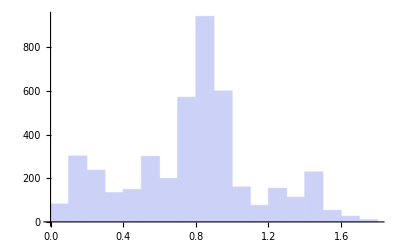

```mathematica
Histogram[kievdist,20]
```

```mathematica
kievtdist=Map[EuclideanDistance[#[[5]],kievtemp]&,xdata];
```

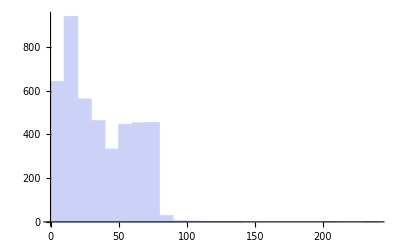

```mathematica
Histogram[kievtdist,20]
```

```mathematica
With[{fromstation = Select[xdata,#[[1]]==kiev &]},
Module[{ ft,dst},
ft=fromstation[[1,5]];
dst=Map[EuclideanDistance[ft,#]&,xdata[[All,5]]];
With[{ddata = Transpose[{xdata,dst}],
maxdist=Max[dst],
fp=fromstation[[1,4]]},
Manipulate[
Module[{dc,dp},
dc = Sort[Select[ddata,#[[2]]≤ distance &],#1[[2]]<#2[[2]]&];
dp=dc[[All,1,4]];
Column[{Show[{wm,
WorldGraphics[{Blue,dp}],
WorldGraphics[{Red,fp}]},ImageSize-> 800],
dc[[All,1,2;;3]]//TableView}]],
{distance,0,maxdist/10}
]]
]
]
```

```mathematica
CountryData[All]
```

{Afghanistan,Albania,Algeria,AmericanSamoa,Andorra,Angola,Anguilla,AntiguaBarbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,BosniaHerzegovina,Botswana,Brazil,BritishVirginIslands,Brunei,Bulgaria,BurkinaFaso,Burundi,Cambodia,Cameroon,Canada,CapeVerde,CaymanIslands,CentralAfricanRepublic,Chad,Chile,China,ChristmasIsland,CocosKeelingIslands,Colombia,Comoros,CookIslands,CostaRica,Croatia,Cuba,Curacao,Cyprus,CzechRepublic,DemocraticRepublicCongo,Denmark,Djibouti,Dominica,DominicanRepublic,EastTimor,Ecuador,Egypt,ElSalvador,EquatorialGuinea,Eritrea,Estonia,Ethiopia,FalklandIslands,FaroeIslands,Fiji,Finland,France,FrenchGuiana,FrenchPolynesia,Gabon,Gambia,GazaStrip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,GuineaBissau,Guyana,Haiti,Honduras,HongKong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,IsleOfMan,Israel,Italy,IvoryCoast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,MarshallIslands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,NewCaledonia,NewZealand,Nicaragua,Niger,Nigeria,Niue,NorfolkIsland,NorthernMarianaIslands,NorthKorea,Norway,Oman,Pakistan,Palau,Panama,PapuaNewGuinea,Paraguay,Peru,Philippines,PitcairnIslands,Poland,Portugal,PuertoRico,Qatar,RepublicCongo,Reunion,Romania,Russia,Rwanda,SaintHelena,SaintKittsNevis,SaintLucia,SaintPierreMiquelon,SaintVincentGrenadines,Samoa,SanMarino,SaoTomePrincipe,SaudiArabia,Senegal,Serbia,Seychelles,SierraLeone,Singapore,SintMaarten,Slovakia,Slovenia,SolomonIslands,Somalia,SouthAfrica,SouthKorea,Spain,SriLanka,Sudan,Suriname,Svalbard,Swaziland,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,TrinidadTobago,Tunisia,Turkey,Turkmenistan,TurksCaicosIslands,Tuvalu,Uganda,Ukraine,UnitedArabEmirates,UnitedKingdom,UnitedStates,UnitedStatesVirginIslands,Uruguay,Uzbekistan,Vanuatu,VaticanCity,Venezuela,Vietnam,WallisFutuna,WestBank,WesternSahara,Yemen,Zambia,Zimbabwe}

```mathematica
CountryData["UnitedStates","FullPolygon"]
```

Polygon[{{{-124.217,40.764},{-124.196,40.8489},{-124.157,40.8968},{-124.136,40.9268},{-124.134,41.008},{-124.18,41.1374},{-124.175,41.1586},{-124.16,41.1808},{-124.133,41.2108},{-124.115,41.2675},{-124.124,41.6203},{-124.121,41.6569},{-124.131,41.6937},{-124.136,41.7226},«4645»,{-124.217,40.6718},{-124.205,40.6607},{-124.193,40.6673},{-124.187,40.6918},{-124.128,40.7729},{-124.122,40.8029},{-124.125,40.8129},{-124.132,40.8251},{-124.155,40.8263},{-124.167,40.8207},{-124.182,40.7618},{-124.197,40.7496},{-124.21,40.7528},{-124.217,40.764}},«481»,{«1»,«60»}}]